```mathematica
mP=1.67*10^(-24); (*g*)
kB=1.38*10^(-16); (*in cgs*)
G=6.67*10^(-8);   (*in cgs*)
h=6.63*10^(-27); (*in cgs*)
Msun=1.989*10^33;
Rsun=6.9598*10^10;
Lsun=3.8418*10^33;
c=3*10^10;   (*cm/s*)
σSB=5.67*10^(-5); 
a=4*σSB/c;   
γ=5/3 ;
mu=0.62;
```

```mathematica
Polinomi=Table[q^i,{i,0,10}];
```

```mathematica
SolarModel0=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\SolarRotation\\BalbusEquation\\SolarModelBS2005-AGS,OP","Table"];

SolarModel=Drop[SolarModel0,1];
SolarModel=Drop[SolarModel,-3];

RadiusMass=Table[{ Rsun*SolarModel[[All,2]][[i]],Msun*SolarModel[[All,1]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusTemp=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,3]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusDens=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,4]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusPress=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,5]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusLumin=Table[{Rsun*SolarModel[[All,2]][[i]],Lsun*SolarModel[[All,6]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusFlux=Table[{Rsun*SolarModel[[All,2]][[i]],Lsun*SolarModel[[All,6]][[i]]/(4*Pi*(RadiusTemp[[i]][[1]])^2)},{i,1,Dimensions[SolarModel][[1]]}];
RadiusGrav=Table[{RadiusMass[[i]][[1]],G*RadiusMass[[i]][[2]]/(RadiusMass[[i]][[1]])^2},{i,1,Dimensions[RadiusMass][[1]]}];
```

```mathematica
RhoN=Interpolation[RadiusDens];
PN=Interpolation[RadiusPress];
TN=Interpolation[RadiusTemp];
Grav=Interpolation[RadiusGrav];

RDown=Rsun*0.1;
RUp=Rsun*0.9;
```

```mathematica
RadiusGravReduced=Select[RadiusGrav,RDown<#[[1]]<RUp&];
RadiusTempReduced=Select[RadiusTemp,RDown<#[[1]]<RUp&];
RadiusPressReduced=Select[RadiusPress,RDown<#[[1]]<RUp&];
RadiusDensReduced=Select[RadiusDens,RDown<#[[1]]<RUp&];
```

```mathematica
RhoFit0=Fit[RadiusDensReduced,Polinomi,q];
RhoFit[x_]=RhoFit0/.{q->x};
Show[Plot[RhoN[r],{r,RDown,RUp}],ListPlot[RadiusDensReduced],Plot[RhoFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","rho (g/cm^3)","Density"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
ρ[R_,z_]=RhoFit[(R^2+z^2)^0.5];
```

```mathematica
TempFit0=Fit[RadiusTempReduced,Polinomi,q];
TempFit[x_]=TempFit0/.{q->x};
Show[Plot[TN[r],{r,RDown,RUp}],ListPlot[RadiusTempReduced],Plot[TempFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","T (K)","Temperature"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
T[R_,z_]=TempFit[(R^2+z^2)^0.5];
```

```mathematica
PressFit0=Fit[RadiusPressReduced,Polinomi,q];
PressFit[x_]=PressFit0/.{q->x};
Show[Plot[PN[r],{r,RDown,RUp}],ListPlot[RadiusPressReduced],Plot[PressFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","P (g/(cm*s^2))","Pressure"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
P[R_,z_]=PressFit[(R^2+z^2)^0.5];
PdR[R_,z_]=D[P[R,z],R];   Pdz[R_,z_]=D[P[R,z],z];
dLogPdLogr[R_,z_]=(P[R,z]/(√(R^2+z^2)))^-1*PressFit'[√(R^2+z^2)];
```

```mathematica
Om0SqList=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\Minimum Pr\\Omega0SqGONG.dat"];
Om0SqFit0=Fit[Om0SqList,Polinomi,q];
Om0SqFit[x_]=Om0SqFit0/.{q->(x/Rsun)};
Show[Plot[Om0SqFit[r],{r,0.5Rsun,0.72Rsun}],ListPlot[Om0SqList,PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","Omega0Sq (rad/s^2)"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
Om2SqList=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\Minimum Pr\\Omega2SqGONG.dat"];
Om2SqFit0=Fit[Om2SqList,Polinomi,q];
Om2SqFit[x_]=Om2SqFit0/.{q->(x/Rsun)};
Show[Plot[Om2SqFit[r],{r,0.5Rsun,0.72Rsun}],ListPlot[Om2SqList,PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","Omega2Sq (rad/s^2)"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
```

```mathematica
Ω[R_,z_]:=√(7.4*10^-12);      dLogΩdLogr:=-0.9;
```

```mathematica
(* THESE APPLY IN THE RADIATIVE ZONE *)

σ[R_,z_]=Log[P[R,z]*ρ[R,z]^(-γ)];
σdR[R_,z_]=D[σ[R,z],R];
σdz[R_,z_]=D[σ[R,z],z];
σdr[R_,z_]=σdR[R,z]*R/(√(R^2+z^2))+σdz[R,z]*z/(√(R^2+z^2));
σdLogr[R_,z_]=√(R^2+z^2)*σdr[R,z];
```

```mathematica
ldR[R_,z_]:=Ω[R,z]*R*(2+R^2/(R^2+z^2)*dLogΩdLogr);
ldz[R_,z_]:=Ω[R,z]*R*(z/(√(R^2+z^2))*dLogΩdLogr);
```

```mathematica
Mu=0.62;   γ=5/3;

kRoss=20; (* Rosseland opacity at 0.7 Rsun*)
χ[R_,z_]=(16*T[R,z]^3*σSB*(γ-1)*Mu*mP)/(3*kRoss*ρ[R,z]^2*kB);   (*this is what Goldreich and Schubert call χ*)
ξrad[R_,z_] = (γ-1)*χ[R,z];   (*this is what Menou and Balbus call ξrad*)

Λ=10^4;    νdyn[R_,z_]=2.2*10^-15*T[R,z]^(5/2)/(ρ[R,z]*Log10[Λ]);   (*dynamic viscosity by Spitzer*)

 νrad[R_,z_]=16/15*(σSB*T[R,z]^4)/(kRoss*ρ[R,z]^2*c^2);   (*radiative viscosity by Menou and Balbus*)
ν[R_,z_]=νrad[R,z]+νdyn[R,z];
```

```mathematica
LastTermGS[R_,z_,kR_,kz_]:=(kz^2/(kR^2+kz^2))*1/(γ*Ω[R,z]^2 ρ[R,z])*((ν[R,z]*(kR^2+kz^2))/Ω[R,z])(PdR[R,z]-kR/kz Pdz[R,z])(kR/kz σdz[R,z]-σdR[R,z])+(2/(γ*Ω[R,z]*R))(kz^2/(kR^2+kz^2))((χ[R,z]*(kR^2+kz^2))/Ω[R,z])(ldR[R,z]-kR/kz ldz[R,z])+1/γ((χ[R,z]*(kR^2+kz^2))/Ω[R,z])((ν[R,z]*(kR^2+kz^2))/Ω[R,z])^2
```

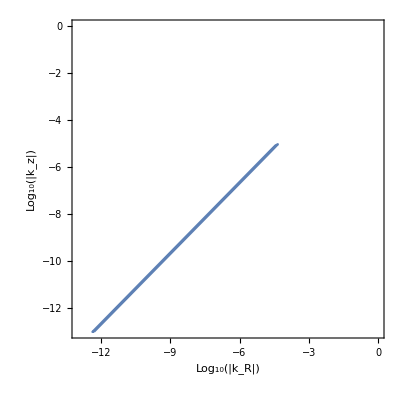
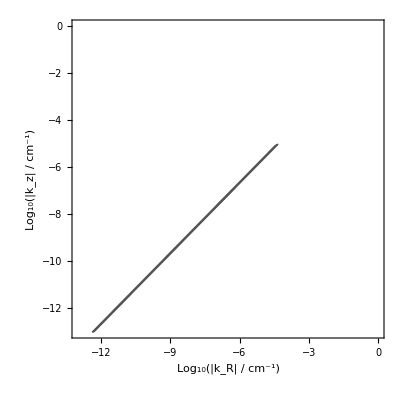
{47.78125,{{(r,θ) = (0.6,Pi
--
36), ν_dyn = 18.2851, ν_rad = 1.2221, Pr = 3.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.6,Pi
--
12), ν_dyn = 18.2851, ν_rad = 1.2221, Pr = 3.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.6,5 Pi
----
 36), ν_dyn = 18.2851, ν_rad = 1.2221, Pr = 3.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.6,7 Pi
----
 36), ν_dyn = 18.2851, ν_rad = 1.2221, Pr = 3.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.6,Pi
--
4), ν_dyn = 18.2851, ν_rad = 1.2221, Pr = 3.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.6,11 Pi
-----
 36), ν_dyn = 18.2851, ν_rad = 1.2221, Pr = 3.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.6,13 Pi
-----
 36), ν_dyn = 18.2851, ν_rad = 1.2221, Pr = 3.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.6,5 Pi
----
 12), ν_dyn = 18.2851, ν_rad = 1.2221, Pr = 3.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.6,17 Pi
-----
 36), ν_dyn = 18.2851, ν_rad = 1.2221, Pr = 3.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{(r,θ) = (0.65,Pi
--
36), ν_dyn = 20.6822, ν_rad = 1.7863, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.65,Pi
--
12), ν_dyn = 20.6822, ν_rad = 1.7863, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.65,5 Pi
----
 36), ν_dyn = 20.6822, ν_rad = 1.7863, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.65,7 Pi
----
 36), ν_dyn = 20.6822, ν_rad = 1.7863, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.65,Pi
--
4), ν_dyn = 20.6822, ν_rad = 1.7863, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.65,11 Pi
-----
 36), ν_dyn = 20.6822, ν_rad = 1.7863, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.65,13 Pi
-----
 36), ν_dyn = 20.6822, ν_rad = 1.7863, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.65,5 Pi
----
 12), ν_dyn = 20.6822, ν_rad = 1.7863, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.65,17 Pi
-----
 36), ν_dyn = 20.6822, ν_rad = 1.7863, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{(r,θ) = (0.7,Pi
--
36), ν_dyn = 21.1306, ν_rad = 2.20016, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.7,Pi
--
12), ν_dyn = 21.1306, ν_rad = 2.20016, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.7,5 Pi
----
 36), ν_dyn = 21.1306, ν_rad = 2.20016, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.7,7 Pi
----
 36), ν_dyn = 21.1306, ν_rad = 2.20016, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.7,Pi
--
4), ν_dyn = 21.1306, ν_rad = 2.20016, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.7,11 Pi
-----
 36), ν_dyn = 21.1306, ν_rad = 2.20016, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.7,13 Pi
-----
 36), ν_dyn = 21.1306, ν_rad = 2.20016, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.7,5 Pi
----
 12), ν_dyn = 21.1306, ν_rad = 2.20016, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.7,17 Pi
-----
 36), ν_dyn = 21.1306, ν_rad = 2.20016, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-}}}

```mathematica
Timing[Table[
Rper=rper*Sin[θper];   zper=rper*Cos[θper];


"(r,θ) = (" <> ToString[rper/Rsun] <> "," <> ToString[θper]  <>"), ν_dyn = "<>ToString[νdyn[Rper,zper]] <> ", ν_rad = " <> ToString[νrad[Rper,zper]] <> (*", ξ_rad = " <> ToString[ScientificForm[ξrad[Rper,zper],2,NumberFormat->(#1<>"*10^"<>#3&)]] <> *)", Pr = " <> ToString[ScientificForm[ν[Rper,zper]/ξrad[Rper,zper],2,NumberFormat->(#1<>"*10^"<>#3&)]] <> "."

RegionPlot[LastTermGS[Rper,zper,10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R > 0, k_z > 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}]
RegionPlot[LastTermGS[Rper,zper,-10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R < 0, k_z > 0"},LabelStyle->Black,BoundaryStyle->{Darker[Gray],Thick},BaseStyle->{FontWeight->"Bold",FontSize->12}]
RegionPlot[LastTermGS[Rper,zper,10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z < 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}]
RegionPlot[LastTermGS[Rper,zper,-10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z < 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}],{rper,0.6Rsun,0.7Rsun,0.05Rsun},{θper,π/36,17*π/36,2*π/36}]]
```